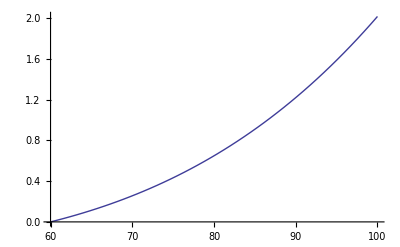

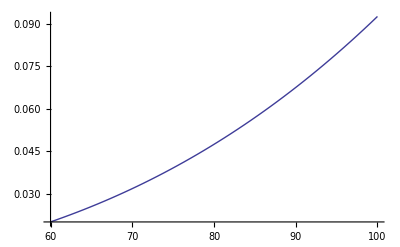

```mathematica
(*Stefan Boltzmann Constant*)
σ = 5.67*10^-8; (*W/m^2K*)
(*Sapphire diameter*)
diam = 0.510; (*mm*)
(*Sapphire surface area*)
sarea = π*(diam/2)^2;

(*Alumina filter temperature*)
aTemp = 60; (*K*)

(*Radiative heat transfer vs sapphire temperature*)
Rad[T_]:= σ*sarea*2*(T^4 - aTemp^4);
(*Cooling power vs sapphire temperature*)
Cool[T_]:= σ*sarea*2*4*T^3;

(*Plot heat transfer*)
Plot[Rad[x], {x, aTemp, 100}]

(*Plot cooling power*)
Plot[Cool[x], {x, aTemp, 100}]
```